```mathematica
(*LIMITS FROM SUPER K*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_?NumericQ]:=(4*ρ0)/(r/r0*(1+r/r0)^2);
```

```mathematica
emax=60*10^-3;(*in GeV*)
```

```mathematica
emin=17.3*10^-3;(*in GeV*)
```

```mathematica
(*ϕ[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)*)
```

```mathematica
(*ϕdet[mpbh_?NumericQ,fpbh_?NumericQ]:=ϕ[mpbh,fpbh]/(4*π*(r0)^2);(*mpbh in g*)*)
```

```mathematica
ϕdet[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[ρ[r],{r,0,rmax},WorkingPrecision->4]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*)
```

```mathematica
(*conversion from GeV to s^-1*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
egdata=Import["egb_v2.dat","Table"];
grahamdata=Import["mono_bound_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];
```

```mathematica
myticks={{{{-7,"10^-7"},{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{12,"10^12"},{13,"10^13"},{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"}},None}};
```

```mathematica
p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-11}},PlotStyle->Red,Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


q=ListPlot[Table[{Log10[10^16*grahamdata[[i,1]]],Log10[grahamdata[[i,2]]]},{i,Length[grahamdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Green],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{15,18},{-5,0}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];
```

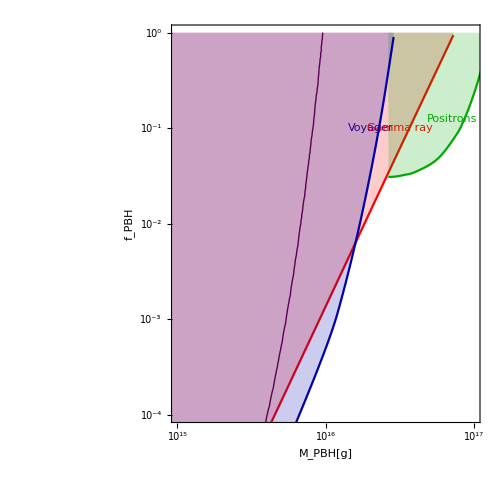

```mathematica
Show[RegionPlot[x<Log10[5*10^14],{x,15,17},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotStyle->Lighter[Red],FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],ContourPlot[{ϕdet[10^x,10^y]==2.9},{x,14,17},{y,0,-7},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Voyager",Darker[Blue]],{16.3,-1.0}],85 Degree]],Graphics[Rotate[Text[Style["Gamma ray",Red],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["Positrons",Darker[Green]],{16.85,-0.9}],75 Degree]],Graphics[Rotate[Text[Style["Evaporation",Black],{14.3,-2.0}],0 Degree]],p,q,r]
```

```mathematica
(*LIMITS FROM SUPER K for Kerr Black hole*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)

(*ρ[r_?NumericQ]:=(4*ρ0)/(r/r0*(1+r/r0)^2);*)
```

```mathematica
ρ[r_]:=ρ0*(r/r0)^-1*((1+(r0/rs))/(1+(r/rs)))^2;
```

```mathematica
emax=60*10^-3;(*in GeV*)
```

```mathematica
emin=17.3*10^-3;(*in GeV*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdet[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ]:=1/(2*π)*NIntegrate[(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1),{e,emin,emax}]*NIntegrate[ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

```mathematica
T[10^17,0]*1000
```

0.105559

```mathematica
T[10^15,0.9999]*1000
```

0.294395

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
egdata=Import["egb_v2.dat","Table"];
grahamdata=Import["mono_bound_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];

pl=ContourPlot[{ϕdet[10^x,10^y]==2.9},{x,14,17},{y,0,-9},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20];
points=Catenate@Cases[Normal@pl,Line[pts_]->pts,Infinity];
```

```mathematica
Export["contour_output_file",points,"Table"];
```

```mathematica
myticks={{{{-9,"10^-9"},{-8,"10^-8"},{-7,"10^-7"},{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{12,"10^12"},{13,"10^13"},{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"}},None}};
```

```mathematica
p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-9}},PlotStyle->Darker[Orange],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

q=ListPlot[Table[{Log10[10^16*grahamdata[[i,1]]],Log10[grahamdata[[i,2]]]},{i,Length[grahamdata]}],PlotRange->{{14,17},{0,-9}},PlotStyle->Darker[Green],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,17},{0,-9}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

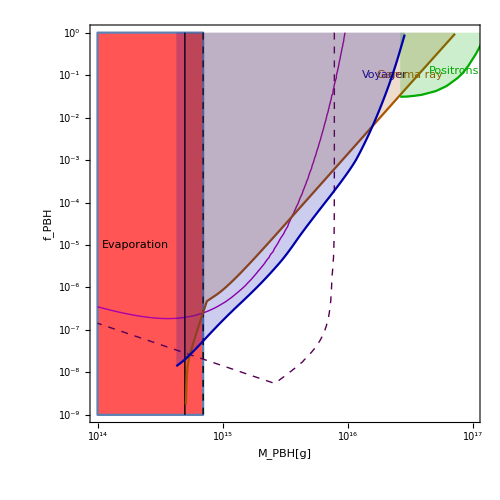

```mathematica
Show[RegionPlot[{x<Log10[7*10^14]},{x,14,17},{y,0,-9},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotStyle->{{Thick,Lighter[Red],Dashed}},FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500],ContourPlot[{x==Log10[7*10^14]},{x,14,17},{y,0,-9},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Black],Dashed}},FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500],ContourPlot[{ϕdet[10^x,10^y,0.9999]==2.9},{x,14,17},{y,0,-9},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple],Dashed}},FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{ϕdet[10^x,10^y,0]==2.9},{x,14,17},{y,0,-9},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Magenta]}},FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{x==Log10[5*10^14]},{x,14,17},{y,0,-9},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Black]}},FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Voyager",Darker[Blue]],{16.3,-1.0}],85 Degree]],Graphics[Rotate[Text[Style["Gamma ray",Darker[Orange]],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["Positrons",Darker[Green]],{16.85,-0.9}],75 Degree]],Graphics[Rotate[Text[Style["Evaporation",Black],{14.3,-5.0}],0 Degree]],p,q,r]//Quiet
```

```mathematica
(*INTEGRAL RESULTS*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.5*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=15*10^3*3.086*10^18;(*in cm*)(*15 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_]:=ρ0*(r/r0)^-1*((1+(r0/rs))/(1+(r/rs)))^2
```

```mathematica
emax=1*10^-3;(*in GeV*)
```

```mathematica
emin=0.5*10^-3;(*in GeV*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));
```

```mathematica
ϕgraham[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)


ϕgrahamkerr[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)

SetDirectory[NotebookDirectory[]];
egdata=Import["egb_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];
femtodata=Import["femtolensing.dat","Table"];

p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-11}},PlotStyle->Red,Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

q=ListPlot[Table[{Log10[10^16*femtodata[[i,1]]],Log10[femtodata[[i,2]]]},{i,Length[femtodata]}],PlotRange->{{14,18},{0,-8}},PlotStyle->{Darker[Orange]},Frame->True,InterpolationOrder-> 2,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

```mathematica
myticks={{{{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{16,"10^16"},{17,"10^17"},{18,"10^18"}},None}};
```

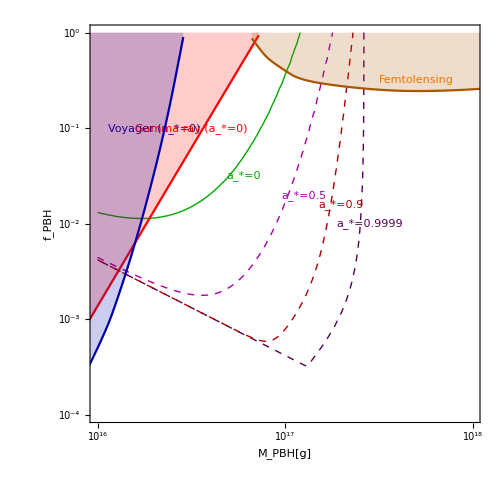

```mathematica
Show[ContourPlot[{ϕgraham[10^x,10^y]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Green]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{ϕgrahamkerr[10^x,10^y,0.9999]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple],Dashed}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{ϕgrahamkerr[10^x,10^y,0.5]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Magenta],Dashed}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->30],ContourPlot[{ϕgrahamkerr[10^x,10^y,0.9]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Red],Dashed}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->50],Graphics[Rotate[Text[Style["Voyager (a_*=0)",Darker[Blue]],{16.3,-1.0}],88 Degree]],Graphics[Rotate[Text[Style["Gamma ray (a_*=0)",Red],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["a_*=0",Darker[Green]],{16.78,-1.5}],70Degree]],Graphics[Rotate[Text[Style["a_*=0.5",Darker[Magenta]],{17.10,-1.7}],75Degree]],Graphics[Rotate[Text[Style["a_*=0.9",Darker[Red]],{17.30,-1.8}],80Degree]],Graphics[Rotate[Text[Style["a_*=0.9999",Darker[Purple]],{17.45,-2.0}],85Degree]],Graphics[Rotate[Text[Style["Femtolensing",Orange],{17.7,-0.5}],10 Degree]],p,q,r]
```

```mathematica
(*Show[ContourPlot[{ϕlaha[10^x,10^y]==4*10^43},{x,16,17.3},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Brown}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],ContourPlot[{ϕlahakerr[10^x,10^y,0.7]==4*10^43},{x,16,17.3},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Voyager",Darker[Blue]],{16.3,-1.0}],85 Degree]],Graphics[Rotate[Text[Style["Gamma ray",Red],{16.5,-1.0}],75 Degree]],p,r]*)
```

```mathematica
(*INTEGRAL RESULTS FOR ISOTHERMAL PROFILE*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.5*10^3*3.086*10^18;(*in cm*)
rs=3.5*10^3*3.086*10^18;(*in cm*)
rmax=15*10^3*3.086*10^18;(*in cm*)(*15 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_]:=ρ0*((1+(r0/rs)^2)/(1+(r/rs)^2))
```

```mathematica
emax=1*10^-3;(*in GeV*)
```

```mathematica
emin=0.5*10^-3;(*in GeV*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));
```

```mathematica
ϕgraham[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)


ϕgrahamkerr[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)

SetDirectory[NotebookDirectory[]];
egdata=Import["egb_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];
femtodata=Import["femtolensing.dat","Table"];

p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-11}},PlotStyle->Red,Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

q=ListPlot[Table[{Log10[10^16*femtodata[[i,1]]],Log10[femtodata[[i,2]]]},{i,Length[femtodata]}],PlotRange->{{14,18},{0,-8}},PlotStyle->{Darker[Orange]},Frame->True,InterpolationOrder-> 2,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

```mathematica
myticks={{{{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{16,"10^16"},{17,"10^17"},{18,"10^18"}},None}};
```

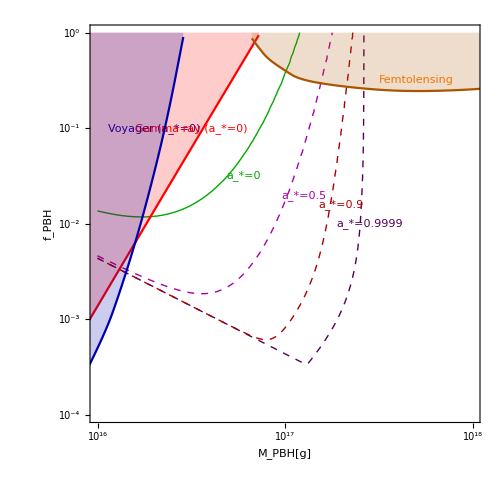

```mathematica
Show[ContourPlot[{ϕgraham[10^x,10^y]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Green]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{ϕgrahamkerr[10^x,10^y,0.9999]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple],Dashed}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{ϕgrahamkerr[10^x,10^y,0.5]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Magenta],Dashed}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->30],ContourPlot[{ϕgrahamkerr[10^x,10^y,0.9]==2*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Red],Dashed}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->50],Graphics[Rotate[Text[Style["Voyager (a_*=0)",Darker[Blue]],{16.3,-1.0}],88 Degree]],Graphics[Rotate[Text[Style["Gamma ray (a_*=0)",Red],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["a_*=0",Darker[Green]],{16.78,-1.5}],70Degree]],Graphics[Rotate[Text[Style["a_*=0.5",Darker[Magenta]],{17.10,-1.7}],75Degree]],Graphics[Rotate[Text[Style["a_*=0.9",Darker[Red]],{17.30,-1.8}],80Degree]],Graphics[Rotate[Text[Style["a_*=0.9999",Darker[Purple]],{17.45,-2.0}],85Degree]],Graphics[Rotate[Text[Style["Femtolensing",Orange],{17.7,-0.5}],10 Degree]],p,q,r]
```

```mathematica
(*Evolution of a_* with time*)



mpbhlist=10^Subdivide[16,18,100];
G=6.707*10^-39;(*In GeV^-2*)
emax=1*10^-3;(*in GeV*)
emin=0.5*10^-3;(*in GeV*)
astarlist={};

Do[
mpbh=mpbhlist[[i]];
T[astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));(*mpbh in g*) 



func1[astar_?NumericQ]:=(mpbh*5.62*10^23)^2*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[astar])/T[astar]]+1)*e,{e,emin,emax},Method->"LocalAdaptive"];
func2[astar_?NumericQ]:=(mpbh*5.62*10^23)/(G*astar)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[astar])/T[astar]]+1),{e,emin,emax},Method->"LocalAdaptive"];


eqn=astar'[t]==(astar[t]*(2*func1[astar[t]]-func2[astar[t]]))/((mpbh*5.62*10^23)^3)*1.52*10^24;(*conversion from GeV to s^-1*)
 bcn=astar[0]==0.9999;

res=NDSolveValue[{eqn,bcn},astar[4*10^17],{t,0,4*10^17}];
AppendTo[astarlist,res];
,{i,Length[mpbhlist]}]//Quiet
```

```mathematica
myticks={{Automatic,None},{{{10^16,"10^16"},{10^17,"10^17"},{10^18,"10^18"}},None}};
```

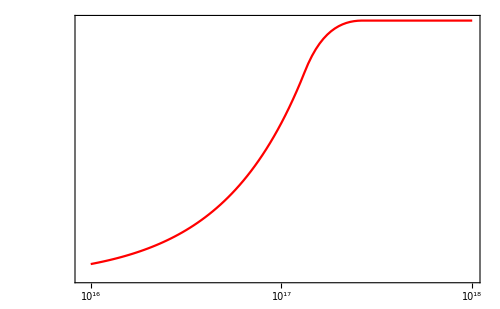

```mathematica
ListLogLogPlot[Table[{mpbhlist[[i]],astarlist[[i]]},{i,Length[mpbhlist]}],Joined->True,PlotStyle->Red,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->500,FrameTicks->myticks]
```

```mathematica
data=Transpose[{N[mpbhlist],astarlist}];
```

```mathematica
f=Interpolation[data,InterpolationOrder->1];
```

```mathematica
astar[mpbh_?NumericQ]:=f[mpbh];
```

```mathematica
(*INTEGRAL RESULTS*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rmax=15*10^3*3.086*10^18;(*in cm*)(*15 kpc is roughly the size of our galaxy*)
```

```mathematica
ρ[r_]:=(4*ρ0)/(r/r0*(1+r/r0)^2);
```

```mathematica
T[mpbh_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar[mpbh]^2)^0.5)/(1+(1-astar[mpbh]^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ]:=astar[mpbh]/(2*G*mpbh*5.62*10^23*(1+(1-astar[mpbh]^2)^0.5));(*mpbh in g*)
```

```mathematica
ϕgraham[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)


ϕgrahamkerr[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh])/T[mpbh]]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)

SetDirectory[NotebookDirectory[]];
egdata=Import["egb_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];
femtodata=Import["femto.dat","Table"];

p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-11}},PlotStyle->Red,Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

q=ListPlot[Table[{Log10[femtodata[[i,1]]],Log10[femtodata[[i,2]]]},{i,Length[femtodata]}],PlotRange->{{14,18},{0,-8}},PlotStyle->{Darker[Orange],Dashed},Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

```mathematica
myticks={{{{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{16,"10^16"},{17,"10^17"},{18,"10^18"}},None}};
```

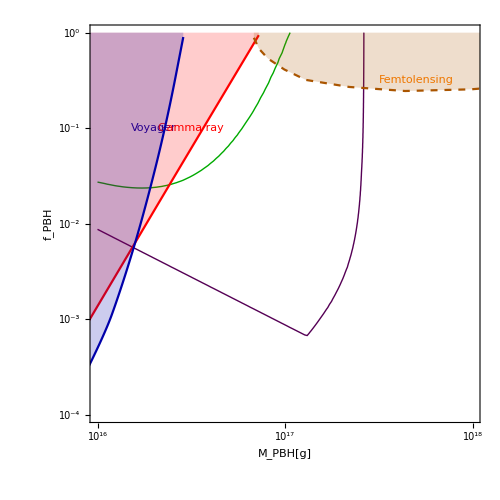

```mathematica
Show[ContourPlot[{ϕgraham[10^x,10^y]==4*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Green]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],ContourPlot[{ϕgrahamkerr[10^x,10^y]==4*10^43},{x,16,18},{y,0,-4},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],Graphics[Rotate[Text[Style["Voyager",Darker[Blue]],{16.3,-1.0}],85 Degree]],Graphics[Rotate[Text[Style["Gamma ray",Red],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["Femtolensing",Orange],{17.7,-0.5}],10 Degree]],p,q,r]
```

```mathematica
(*Evolution of a_* with time*)



mpbhlist=10^Subdivide[14,17,100];
G=6.707*10^-39;(*In GeV^-2*)
emax=50*10^-3;(*in GeV*)
emin=17.3*10^-3;(*in GeV*)
astarlist={};

Do[
mpbh=mpbhlist[[i]];
T[astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));(*mpbh in g*) 



func1[astar_?NumericQ]:=(mpbh*5.62*10^23)^2*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[astar])/T[astar]]+1)*e,{e,emin,emax},Method->"LocalAdaptive"];
func2[astar_?NumericQ]:=(mpbh*5.62*10^23)/(G*astar)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[astar])/T[astar]]+1),{e,emin,emax},Method->"LocalAdaptive"];


eqn=astar'[t]==(astar[t]*(2*func1[astar[t]]-func2[astar[t]]))/((mpbh*5.62*10^23)^3)*1.52*10^24;(*conversion from GeV to s^-1*)
 bcn=astar[0]==0.9999;

res=NDSolveValue[{eqn,bcn},astar[4*10^17],{t,0,4*10^17}];
AppendTo[astarlist,res];
,{i,Length[mpbhlist]}]//Quiet
```

```mathematica
myticks={{Automatic,None},{{{10^14,"10^14"},{10^15,"10^15"},{10^16,"10^16"},{10^17,"10^17"}},None}};
```

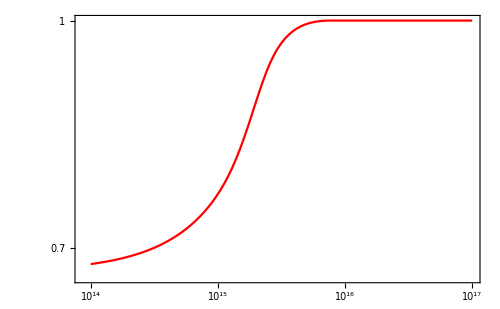

```mathematica
ListLogLogPlot[Table[{mpbhlist[[i]],astarlist[[i]]},{i,Length[mpbhlist]}],Joined->True,PlotStyle->Red,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->500,FrameTicks->myticks]
```

```mathematica
data=Transpose[{N[mpbhlist],astarlist}];
```

```mathematica
f=Interpolation[data,InterpolationOrder->1];
```

```mathematica
astar[mpbh_?NumericQ]:=f[mpbh];
```

```mathematica
(*LIMITS FROM SUPER K for Kerr Black hole*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
```

```mathematica
ρ[r_?NumericQ]:=(4*ρ0)/(r/r0*(1+r/r0)^2);
```

```mathematica
T[mpbh_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar[mpbh]^2)^0.5)/(1+(1-astar[mpbh]^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ]:=astar[mpbh]/(2*G*mpbh*5.62*10^23*(1+(1-astar[mpbh]^2)^0.5));

ϕdet[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh])/T[mpbh]]+1),{e,emin,emax}]*NIntegrate[ρ[r],{r,0,rmax},WorkingPrecision->4]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
egdata=Import["egb_v2.dat","Table"];
grahamdata=Import["mono_bound_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];
```

```mathematica
myticks={{{{-8,"10^-8"},{-7,"10^-7"},{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{12,"10^12"},{13,"10^13"},{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"}},None}};
```

```mathematica
p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-8}},PlotStyle->Red,Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

q=ListPlot[Table[{Log10[10^16*grahamdata[[i,1]]],Log10[grahamdata[[i,2]]]},{i,Length[grahamdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Green],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,17},{0,-8}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

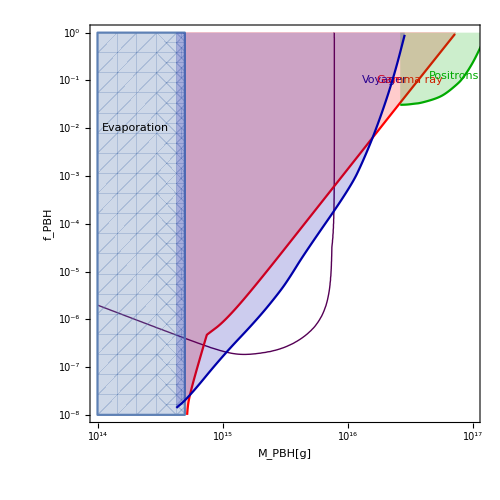

```mathematica
Show[ContourPlot[{ϕdet[10^x,10^y]==2.9},{x,14,17},{y,0,-8},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],RegionPlot[x<Log10[5*10^14],{x,14,17},{y,0,-8}],Graphics[Rotate[Text[Style["Voyager",Darker[Blue]],{16.3,-1.0}],85 Degree]],Graphics[Rotate[Text[Style["Gamma ray",Red],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["Positrons",Darker[Green]],{16.85,-0.9}],75 Degree]],Graphics[Rotate[Text[Style["Evaporation",Black],{14.3,-2.0}],0 Degree]],p,q,r]
```

```mathematica
6.707*10^-39*+60*10^-3*10^16*5.62*10^23
```

2.2616

```mathematica
6.707*10^-39*1*10^-3*10^16*5.62*10^23
```

0.0376933

```mathematica
(*Calculation for Ptloemy*)
```

```mathematica
Nt=2*10^25;(*number of tritium atoms in 100 g tritium*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.5*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=150*10^3*3.086*10^18;(*in cm*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
sigma=10^-45;(*in cm^2*)
```

```mathematica
tage=4.32*10^17;
τ[mpbh_?NumericQ]:=3.28*10^-27*mpbh^3;
```

```mathematica
p[mpbh_?NumericQ]:=Exp[-tage/τ[mpbh]];
```

```mathematica
ρ[l_,ψ_]:=ρ0*(((r0^2+l^2-2*r0*l*Cos[ψ])^0.5)/r0)^-1*((1+(r0/rs))/(1+(((r0^2+l^2-2*r0*l*Cos[ψ])^0.5)/rs)))^2;
lmax[ψ_]:=r0*Cos[ψ]+(rmax^2-r0^2*Sin[ψ]^2)^0.5;
```

```mathematica
emax=50*10^-9;(*in GeV*)
```

```mathematica
emin=1*10^-9;(*in GeV*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdet[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ,ψ_?NumericQ]:=NIntegrate[1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1),{e,emin,emax}]*1/2*NIntegrate[ρ[l,ψ],{l,0,lmax[ψ]}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24*p[mpbh];
```

```mathematica
ϕdetf[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ]:=0.5*NIntegrate[ϕdet[mpbh,fpbh,astar,ψ]*Sin[ψ],{ψ,0,π},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
event[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ]:=Nt*ϕdetf[mpbh,fpbh,astar]*sigma*3.15*10^7;
```

```mathematica
event[10^18,1,0]
```

2.38947×10^-23

```mathematica
ϕdetf[10^20,1,0]
```

3.13293×10^-9

```mathematica
(*LIMITS FROM SUPER K WITH INTERPOLATED GREYBODY FACTOR*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_?NumericQ]:=(4*ρ0)/(r/r0*(1+r/r0)^2);
```

```mathematica
emax=50*10^-3;(*in GeV*)
```

```mathematica
emin=17.3*10^-3;(*in GeV*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
greybodydata=Import["interpolation.dat","Table"];
```

```mathematica
func=Interpolation[greybodydata,InterpolationOrder->2];
```

```mathematica
f[x_]:=func[x];
```

```mathematica
ϕdet[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(27*x^2*f[x])/(Exp[8*π*x]+1)*1/(G*mpbh*5.62*10^23),{x,G*mpbh*5.62*10^23*emin,G*mpbh*5.62*10^23*emax}]*NIntegrate[ρ[r],{r,0,rmax},WorkingPrecision->4]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

```mathematica
egdata=Import["egb_v2.dat","Table"];
grahamdata=Import["mono_bound_v2.dat","Table"];
voyagerdata=Import["voyagerred_v2.dat","Table"];
```

```mathematica
myticks={{{{-7,"10^-7"},{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{12,"10^12"},{13,"10^13"},{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"}},None}};
```

```mathematica
p=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,17},{0,-11}},PlotStyle->Red,Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


q=ListPlot[Table[{Log10[10^16*grahamdata[[i,1]]],Log10[grahamdata[[i,2]]]},{i,Length[grahamdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Green],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


r=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,17},{0,-7}},PlotStyle->Darker[Blue],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

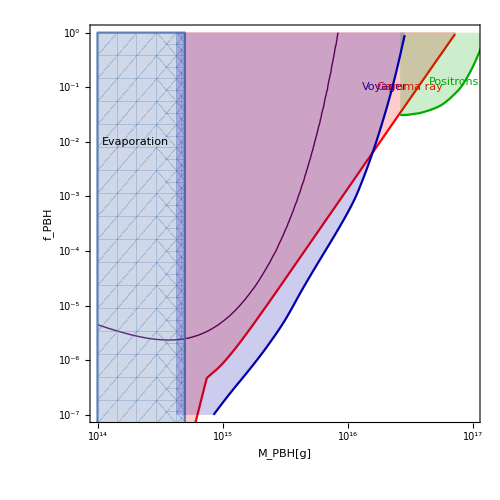

```mathematica
Show[ContourPlot[{ϕdet[10^x,10^y]==2.9},{x,14,17},{y,0,-7},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],RegionPlot[x<Log10[5*10^14],{x,14,17},{y,0,-8}],Graphics[Rotate[Text[Style["Voyager",Darker[Blue]],{16.3,-1.0}],85 Degree]],Graphics[Rotate[Text[Style["Gamma ray",Red],{16.5,-1.0}],75 Degree]],Graphics[Rotate[Text[Style["Positrons",Darker[Green]],{16.85,-0.9}],75 Degree]],Graphics[Rotate[Text[Style["Evaporation",Black],{14.3,-2.0}],0 Degree]],p,q,r]
```

```mathematica
(*SPECTRUM ANALYSIS FOR NON ROTATING BLACKHOLE*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_?NumericQ]:=(4*ρ0)/(r/r0*(1+r/r0)^2);
```

```mathematica
ϕdet[mpbh_?NumericQ,fpbh_?NumericQ,e_?NumericQ]:=1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1)*1.52*10^24*10^-3*NIntegrate[ρ[r],{r,0,rmax},WorkingPrecision->4]/(mpbh*5.62*10^23)*fpbh; (*mpbh in g*) (*conversion from GeV to s^-1*)(*conversion from GeV^-1 to MeV^-1*)
```

```mathematica
myticks={{Automatic,None},{{{-4,"0.1"},{-3,"1"},{-2,"10"},{-1,"100"}},None}};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
atmnudata=Import["atm.dat","Table"];
ppdata=Import["pp.dat","Table"];
borondata=Import["boron.dat","Table"];
hepdata=Import["hep.dat","Table"];
srndata=Import["srn.dat","Table"];

p=ListLogPlot[Table[{Log10[10^-3*atmnudata[[i,1]]],atmnudata[[i,2]]},{i,Length[atmnudata]}],PlotRange->{{-4,-1},{10^12,10^-4}},PlotStyle->{Blue,Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"atmospheric (ν̄)_e"},{0.78,0.95}]];

q=ListLogPlot[Table[{Log10[10^-3*ppdata[[i,1]]],ppdata[[i,2]]},{i,Length[ppdata]}],PlotRange->{{-4,-1},{10^12,10}},PlotStyle->{Darker[Green],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"pp ν_e"},{0.73,0.90}]];

r=ListLogPlot[Table[{Log10[10^-3*borondata[[i,1]]],borondata[[i,2]]},{i,Length[borondata]}],PlotRange->{{-4,-1},{10^12,10}},PlotStyle->{Darker[Orange],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"8_B ν_e"},{0.73,0.85}]];

s=ListLogPlot[Table[{Log10[10^-3*hepdata[[i,1]]],hepdata[[i,2]]},{i,Length[hepdata]}],PlotRange->{{-4,-1},{10^12,10}},PlotStyle->{Darker[Purple],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"hep ν_e"},{0.74,0.80}]];

t=ListLogPlot[Table[{Log10[10^-3*srndata[[i,1]]],srndata[[i,2]]},{i,Length[srndata]}],PlotRange->{{-4,-1},{10^12,10^-4}},PlotStyle->{Darker[Magenta],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"SRN"},{0.73,0.70}]];
```

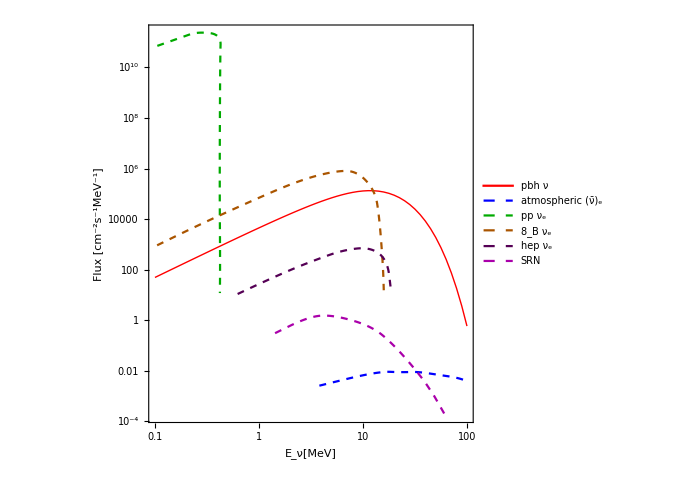

```mathematica
Show[ListLogPlot[{Table[{x,ϕdet[2*10^15,1,10^x]},{x,-4,-1,0.05}]},PlotRange->{{-4,-1},{10^12,10^-4}},Joined-> True,PlotStyle->{{Thick,Red}},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotRange->{{-4,-1},{10^6,10^-4}},FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},AxesOrigin->{-4,Automatic},ImageSize->500,AspectRatio->1,PlotLegends->Placed[{"pbh ν"},{0.75,0.75}]],p,q,r,s,t]
```

```mathematica
(*LogPlot[ϕdet[2*10^15,1,10^x],{x,-4,-1},PlotRange->{{-4,-1},{10^6,10^-4}},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["Log_10[E_ν[GeV]]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},AxesOrigin->{-4,Automatic},ImageSize->500,AspectRatio->1]*)
```

```mathematica
(*SPECTRUM ANALYSIS FOR  ROTATING BLACKHOLE*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_?NumericQ]:=(4*ρ0)/(r/r0*(1+r/r0)^2);
```

```mathematica
astar=0.9;
```

```mathematica
T[mpbh_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));(*mpbh in g*)
```

```mathematica
ϕdet[mpbh_?NumericQ,fpbh_?NumericQ,e_?NumericQ]:=1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh])/T[mpbh]]+1)*1.52*10^24*10^-3*NIntegrate[ρ[r],{r,0,rmax},WorkingPrecision->4]/(mpbh*5.62*10^23)*fpbh; (*mpbh in g*) (*conversion from GeV to s^-1*)(*conversion from GeV^-1 to MeV^-1*)
```

```mathematica
myticks={{Automatic,None},{{{-4,"0.1"},{-3,"1"},{-2,"10"},{-1,"100"}},None}};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
atmnudata=Import["atm.dat","Table"];
ppdata=Import["pp.dat","Table"];
borondata=Import["boron.dat","Table"];
hepdata=Import["hep.dat","Table"];
srndata=Import["srn.dat","Table"];

p=ListLogPlot[Table[{Log10[10^-3*atmnudata[[i,1]]],atmnudata[[i,2]]},{i,Length[atmnudata]}],PlotRange->{{-4,-1},{10^12,10^-4}},PlotStyle->{Blue,Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"atmospheric (ν̄)_e"},{0.78,0.95}]];

q=ListLogPlot[Table[{Log10[10^-3*ppdata[[i,1]]],ppdata[[i,2]]},{i,Length[ppdata]}],PlotRange->{{-4,-1},{10^12,10}},PlotStyle->{Darker[Green],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"pp ν_e"},{0.73,0.90}]];

r=ListLogPlot[Table[{Log10[10^-3*borondata[[i,1]]],borondata[[i,2]]},{i,Length[borondata]}],PlotRange->{{-4,-1},{10^12,10}},PlotStyle->{Darker[Orange],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"8_B ν_e"},{0.73,0.85}]];

s=ListLogPlot[Table[{Log10[10^-3*hepdata[[i,1]]],hepdata[[i,2]]},{i,Length[hepdata]}],PlotRange->{{-4,-1},{10^12,10}},PlotStyle->{Darker[Purple],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"hep ν_e"},{0.74,0.80}]];

t=ListLogPlot[Table[{Log10[10^-3*srndata[[i,1]]],srndata[[i,2]]},{i,Length[srndata]}],PlotRange->{{-4,-1},{10^12,10^-4}},PlotStyle->{Darker[Magenta],Dashed},Frame->True,FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],InterpolationOrder->2,Joined->True,PlotRangePadding->None,PlotLegends->Placed[{"SRN"},{0.73,0.70}]];
```

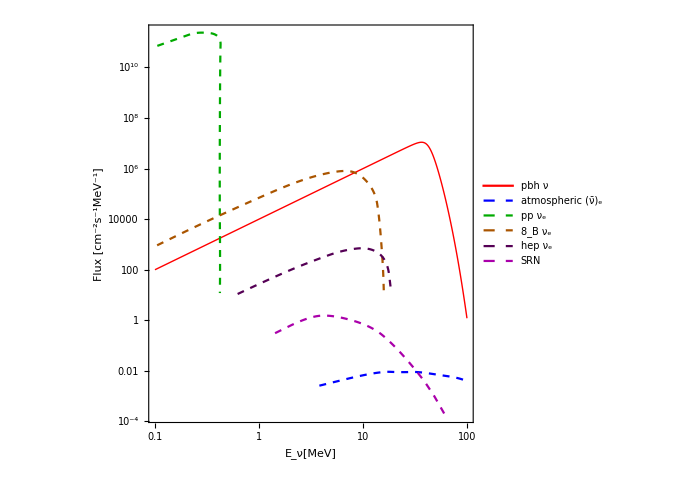

```mathematica
Show[ListLogPlot[{Table[{x,ϕdet[2*10^15,1,10^x]},{x,-4,-1,0.005}]},PlotRange->{{-4,-1},{10^12,10^-4}},Joined-> True,PlotStyle->{{Thick,Red}},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotRange->{{-4,-1},{10^6,10^-4}},FrameTicks->myticks,FrameLabel->{Style["E_ν[MeV]",FontSize->20,Bold],Style["Flux \ [cm^-2s^-1MeV^-1]",FontSize->20,Bold]},AxesOrigin->{-4,Automatic},ImageSize->500,AspectRatio->1,PlotLegends->Placed[{"pbh ν"},{0.75,0.75}]],p,q,r,s,t]
```

```mathematica
(*LIMITS FROM SOLAR NEUTRINO*)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.2*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)(*16 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_]:=ρ0*(r/r0)^-1*((1+(r0/rs))/(1+(r/rs)))^2;
```

```mathematica
emax=15*10^-3;(*in GeV*)
```

```mathematica
emin=0.1*10^-3;(*in GeV*)
```

```mathematica
ϕdet[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24; (*mpbh in g*)
```

```mathematica
(*conversion from GeV to s^-1*)
```

```mathematica
myticks={{{{-7,"10^-7"},{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"10^0"}},None},{{{12,"10^12"},{13,"10^13"},{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"}},None}};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {8.05187×10^-7}. NIntegrate obtained 1.52202×10^25 and 5.97536×10^24 for the integral and error estimates.

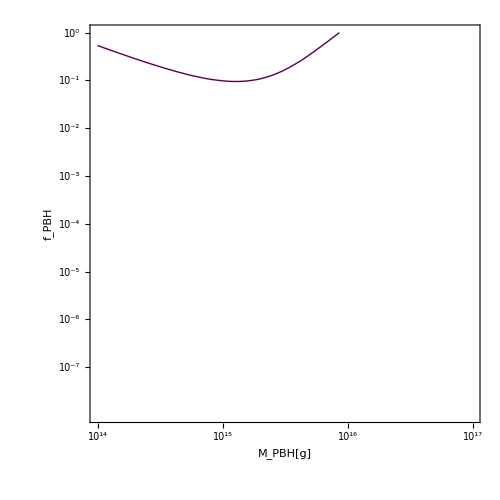

```mathematica
ContourPlot[{ϕdet[10^x,10^y]==(0.040^2+0.060^2)^0.5*10^6},{x,14,17},{y,0,-8},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Darker[Purple]}},FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
(*GW*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
```

```mathematica
c=3*10^8;(*in SI*)
```

```mathematica
deltamin[M_]:=3*(2*G*M*10^-3)/c^2;(*M in g*)
```

```mathematica
fgw[m1_,m2_,Δ_]:=1/π*((G*2*(m1+m2)*10^-3)/Δ^3)^0.5;(*in Hz*)(*m1,m2 in g*)
```

```mathematica
fgw[4*10^6*10^33,10^20,3.6*10^10]
```

0.00107648

```mathematica
agwdl[m1_,m2_,Δ_]:=(4*G^2*m1*m2*10^-6)/(c^4*Δ)*3.24*10^-23; (*in Mpc*)
```

```mathematica
agwdl[4*10^6*10^33,10^20,3.6*10^10]
```

7.90914×10^-34

```mathematica
fgw[30*2*10^33,10^20,deltamin[30*2*10^33]]
```

206.645

```mathematica
agwdl[30*2*10^33,10^20,deltamin[30*2*10^33]]
```

1.6008×10^-33

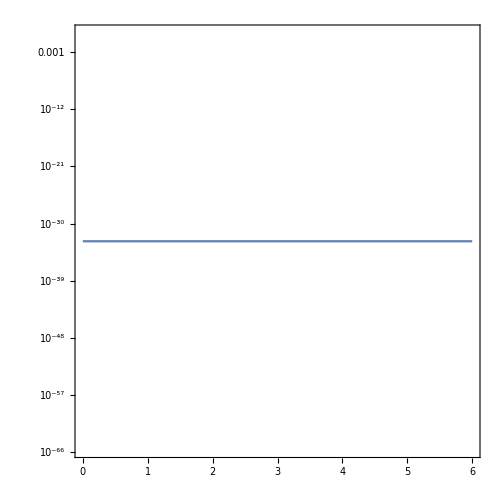

```mathematica
LogPlot[agwdl[2*10^33*10^x,10^20,deltamin[2*10^33*10^x]],{x,0,6},Frame->True,ImageSize->500,AspectRatio->1]
```

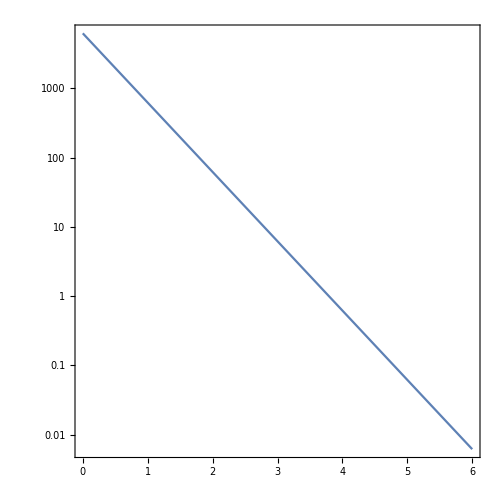

```mathematica
LogPlot[fgw[2*10^33*10^x,10^20,deltamin[2*10^33*10^x]],{x,0,6},Frame->True,ImageSize->500,AspectRatio->1]
```

```mathematica
(*********************************************************************)
```

```mathematica
G=6.674*10^-11;(* in SI*)
```

```mathematica
H0=2.2*10^-18;(*in s^-1*)
omegadm=0.258;
c=3*10^8;(*in SI*)
t0=13.7*10^9*3.154*10^7;(*in s*)

xbar[mpbh_,fpbh_]:=1/((1+3365)*fpbh^(1/3))*((8*π*G)/(3*H0^2)*(mpbh*10^-3)/omegadm)^(1/3)(* in m, mpbh in g*)
```

```mathematica
tc[mpbh_,fpbh_]:=3/170*(c^5*xbar[mpbh,fpbh]^4*fpbh^(25/3))/((G*mpbh*10^-3)^3);(*in s*)
```

```mathematica
T[mpbh_,fpbh_]:=3/170*(c^5*xbar[mpbh,fpbh]^4)/((G*mpbh*10^-3)^3*fpbh^4);(*in s*)
omegalambda=0.692;
omegam=0.308;
```

```mathematica
omegar=5.38*10^-5;
```

```mathematica
t=t0-1/H0*NIntegrate[1/((1+z)*(omegalambda+omegam*(1+z)^3+omegar(1+z)^4)^0.5),{z,0,0.05}];
```

```mathematica
R[mpbh_,fpbh_]:=(3*H0^2)/(8*π*G)*(fpbh*omegadm)/(mpbh*10^-3)*If[t<tc[mpbh,fpbh],3/58*1/t*((t/T[mpbh,fpbh])^(3/37)-(t/T[mpbh,fpbh])^(3/8)),3/58*1/t*(t/T[mpbh,fpbh])^(3/8)*((t/T[mpbh,fpbh])^(-29/56)*fpbh^(-29/8)-1)]*(3.24*10^-26)^-3*(3.17*10^-8)^-1;(*in Gpc^-3 yr^-1*)
```

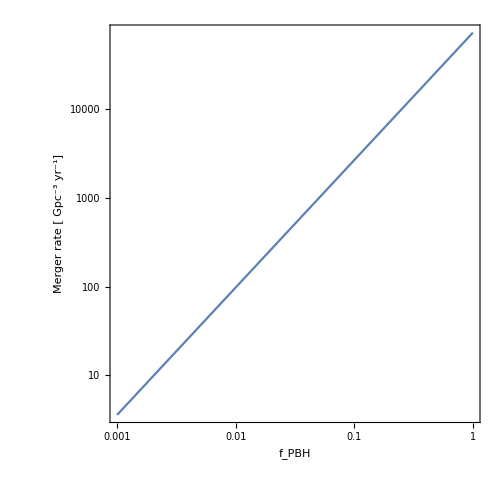

```mathematica
LogLogPlot[R[30*2*10^33,x],{x,10^-3,1},Frame->True,AspectRatio->1,ImageSize->500,PlotRange->All,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["f_PBH",FontSize->20,Bold],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->20,Bold]}]
```

```mathematica
mc=(23.2*2.59)^(3/5)/(23.2+2.59)^(1/5);(*chirp mass for GW190814*)
```

```mathematica
FindRoot[R[6.1*2*10^33,10^x]==23,{x,0}]
```

{x→-2.85575}

```mathematica
myticks={{{{-3,"10^-3",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[3*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[5*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[7*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{Log10[9*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[3*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[5*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[7*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{Log10[9*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[3*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[5*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[7*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}},{Log10[9*10^-1],"",{0.010,0}},{0,"10^0",{0.020,0}}},{{-3,"",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[3*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[5*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[7*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{Log10[9*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[3*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[5*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[7*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{Log10[9*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[3*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[5*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[7*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}},{Log10[9*10^-1],"",{0.010,0}},{0,"",{0.020,0}}}},

{{{Log10[2*10^32],"0.1",{0.020,0}},{Log10[2*2*10^32],"",{0.010,0}},{Log10[3*2*10^32],"",{0.010,0}},{Log10[4*2*10^32],"",{0.010,0}},{Log10[5*2*10^32],"",{0.010,0}},{Log10[6*2*10^32],"",{0.010,0}},{Log10[7*2*10^32],"",{0.010,0}},{Log10[8*2*10^32],"",{0.010,0}},{Log10[9*2*10^32],"",{0.010,0}},{Log10[2*10^33],"1",{0.020,0}},{Log10[2*2*10^33],"",{0.010,0}},{Log10[3*2*10^33],"",{0.010,0}},{Log10[4*2*10^33],"",{0.010,0}},{Log10[5*2*10^33],"",{0.010,0}},{Log10[6*2*10^33],"",{0.010,0}},{Log10[7*2*10^33],"",{0.010,0}},{Log10[8*2*10^33],"",{0.010,0}},{Log10[9*2*10^33],"",{0.010,0}},{Log10[2*10^34],"10",{0.020,0}},{Log10[2*2*10^34],"",{0.010,0}},{Log10[3*2*10^34],"",{0.010,0}},{Log10[4*2*10^34],"",{0.010,0}},{Log10[5*2*10^34],"",{0.010,0}},{Log10[6*2*10^34],"",{0.010,0}},{Log10[7*2*10^34],"",{0.010,0}},{Log10[8*2*10^34],"",{0.010,0}},{Log10[9*2*10^34],"",{0.010,0}},{Log10[2*10^35],"100",{0.020,0}}},{{Log10[2*10^32],"",{0.020,0}},{Log10[2*2*10^32],"",{0.010,0}},{Log10[3*2*10^32],"",{0.010,0}},{Log10[4*2*10^32],"",{0.010,0}},{Log10[5*2*10^32],"",{0.010,0}},{Log10[6*2*10^32],"",{0.010,0}},{Log10[7*2*10^32],"",{0.010,0}},{Log10[8*2*10^32],"",{0.010,0}},{Log10[9*2*10^32],"",{0.010,0}},{Log10[2*10^33],"",{0.020,0}},{Log10[2*2*10^33],"",{0.010,0}},{Log10[3*2*10^33],"",{0.010,0}},{Log10[4*2*10^33],"",{0.010,0}},{Log10[5*2*10^33],"",{0.010,0}},{Log10[6*2*10^33],"",{0.010,0}},{Log10[7*2*10^33],"",{0.010,0}},{Log10[8*2*10^33],"",{0.010,0}},{Log10[9*2*10^33],"",{0.010,0}},{Log10[2*10^34],"",{0.020,0}},{Log10[2*2*10^34],"",{0.010,0}},{Log10[3*2*10^34],"",{0.010,0}},{Log10[4*2*10^34],"",{0.010,0}},{Log10[5*2*10^34],"",{0.010,0}},{Log10[6*2*10^34],"",{0.010,0}},{Log10[7*2*10^34],"",{0.010,0}},{Log10[8*2*10^34],"",{0.010,0}},{Log10[9*2*10^34],"",{0.010,0}},{Log10[2*10^35],"",{0.020,0}}}}};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

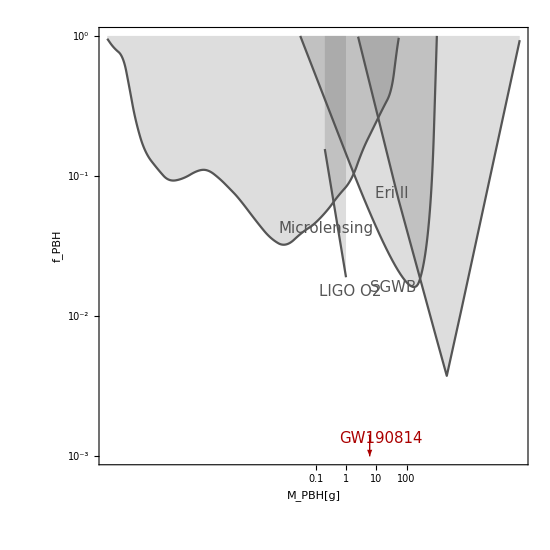

```mathematica
o1data=Import["o1.dat","Table"];
o1datamodi=10^o1data;
o2data=Import["o2.dat","Table"];
machodata=Import["macho.dat","Table"];
dwarfdata=Import["ufd_v2.dat","Table"];

a16=ListPlot[Table[{Log10[2*10^33*o2data[[i,1]]],Log10[o2data[[i,2]]]},{i,Length[o2data]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];

a18=ListPlot[Table[{Log10[2*10^33*o1datamodi[[i,1]]],Log10[o1datamodi[[i,2]]]},{i,Length[o1datamodi]}],PlotRange->{{Log10[2*10^32],Log10[2*10^35]},{0,-3}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.004]],Joined->True,InterpolationOrder-> 2,AspectRatio->1,ImageSize->550,FrameLabel->{Style["M_PBH[g]",FontSize->20],Style["f_PBH",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks];

a4=ListPlot[Table[{Log10[10^16*machodata[[i,1]]],Log10[machodata[[i,2]]]},{i,Length[machodata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];

a10=ListPlot[Table[{Log10[10^16*dwarfdata[[i,1]]],Log10[dwarfdata[[i,2]]]},{i,Length[dwarfdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];
p=Show[a18,a16,a4,a10,Graphics[{Darker[Red],Thick,Line[{{Log10[6.1*2*10^33]-0.04,-2.85575},{Log10[6.1*2*10^33]+0.04,-2.85575}}]}],Graphics[{Arrowheads[0.025],Darker[Red],Arrow[{{Log10[6.1*2*10^33],-2.85575},{Log10[6.1*2*10^33],-2.85575-0.15}}]}],Graphics[Rotate[Text[Style["LIGO O2",Darker[Gray],FontSize->15],{33.45,-1.83}],0 Degree]],Graphics[Rotate[Text[Style["SGWB",Darker[Gray],FontSize->15],{34.85,-1.8}],0 Degree]],Graphics[Rotate[Text[Style["Eri II",Darker[Gray],FontSize->15],{34.8,-1.13}],0 Degree]],Graphics[Rotate[Text[Style["Microlensing",Darker[Gray],FontSize->15],{32.64,-1.38}],12 Degree]],Graphics[Rotate[Text[Style["GW190814",Darker[Red],FontSize->15],{34.44,-2.88}],0 Degree]]]
```

```mathematica
(*********************************************************************)
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
G=6.674*10^-11;(* in SI*)
```

```mathematica
H0=2.197*10^-18;(*in s^-1*)
omegadm=0.27;
t0=14*10^9*3.154*10^7;(*in s*)


npbh[mpbh_,fpbh_]:=(3*H0^2)/(8*π*G)*(fpbh*omegadm)/(mpbh*10^-3);(*in m^-3*)
```

```mathematica
(*npbh[mpbh_,fpbh_]:=(fpbh*0.01*2*10^30*(3.086*10^16)^-3)/(mpbh*10^-3);(*in m^-3*)*)
ymax[mpbh_,fpbh_]:=((4*π)/3*npbh[mpbh,fpbh])^(-1/3);(*mpbh in g*)(*in m*)
```

```mathematica
T[mpbh_,fpbh_]:=3/170*1/((GN*mpbh*5.62*10^23)^3)*(3/(4*π*(1+3450)*fpbh)*ymax[mpbh,fpbh]*5.06*10^15)^4*(1.52*10^24)^-1;(*mpbh in g*)(*in s*)
tc[mpbh_,fpbh_]:=T[mpbh,fpbh]*((4*π*fpbh)/3)^(37/3);
```

```mathematica
R[mpbh_,fpbh_]:=3/58*npbh[mpbh,fpbh]*(t0/T[mpbh,fpbh])^(3/8)*1/t0*If[t0<tc[mpbh,fpbh],1/(t0/T[mpbh,fpbh])^(75/296)-1,1/(((4*π*fpbh)/3)^(25/8)*(t0/tc[mpbh,fpbh])^(25/56))-1]*(3.24*10^-26)^-3*(3.17*10^-8)^-1;(*in Gpc^-3 yr^-1*)
```

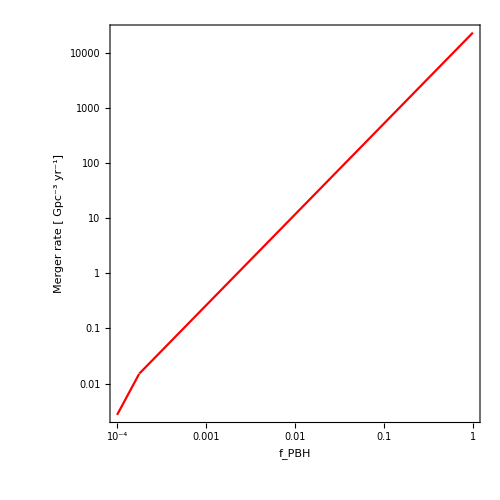

```mathematica
LogLogPlot[R[30*2*10^33,x],{x,10^-4,1},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["f_PBH",FontSize->20,Bold],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->20,Bold]},PlotStyle->Red]
```

```mathematica
omegalambda=(1-omegam-omegar);
omegam=0.307;
omegar=9.061*10^-5;
```

```mathematica
t[z_]:=t0-1/H0*NIntegrate[1/((1+p)*(omegalambda+omegam*(1+p)^3+omegar(1+p)^4)^0.5),{p,0,z}];
```

```mathematica
R2[mpbh_,fpbh_,z_]:=3/58*npbh[mpbh,fpbh]*(t[z]/T[mpbh,fpbh])^(3/8)*1/t[z]*If[t[z]<tc[mpbh,fpbh],1/(t0/T[mpbh,fpbh])^(75/296)-1,1/(((4*π*fpbh)/3)^(25/8)*(t0/tc[mpbh,fpbh])^(25/56))-1]*(3.24*10^-26)^-3*(3.17*10^-8)^-1;(*in Gpc^-3 yr^-1*)
```

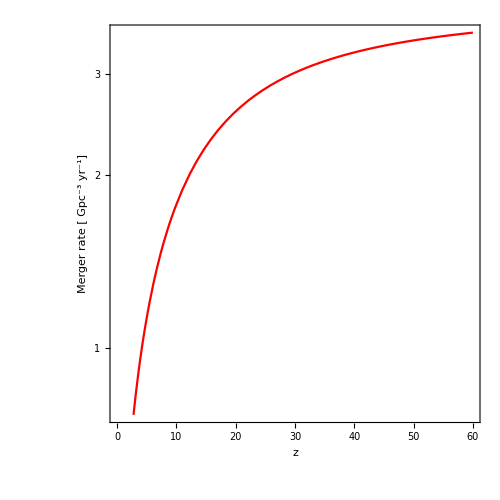

```mathematica
LogPlot[R2[30*2*10^33,10^-3,z],{z,0,60},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20,Bold],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->20,Bold]},PlotStyle->Red]
```